```mathematica
NotebookEvaluate[NotebookDirectory[]<>"NOMexplicitPhaseFieldMain.nb"];
```

```mathematica
(*Create the model*)
xmin={0.,0.};xmax=10^-3{1.,1.};{width,height}=xmax-xmin;dx=10^-3 0.01;(*100x100 particles.*)
coord=GridDomain[xmin,xmax,dx];
vol=ConstantArray[dx^2,Length[coord]];
Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;
(*material parameters for linear elasticity*)
Es=210. 10^9;mu=0.3;rho=7800.;pmass=rho vol;etype=2;
Gc=2700.;(*critical energy release rate*)
 pfModulus=4.;pfModulusT=1.;(*phase field modulus.*)
{bulkK,shearG}=PlaneStress[Es,mu,True];
penCoef=1.;
numNei=8;
NeiList=Nearest[coord->Automatic,coord,numNei+1];(*find the k-nearest neighbors for each particle*)
WeiF[r_]:=1./r^2;
coord0=coord;mesh1=MyDelaunayMesh[coord0];(*mesh for postprocess only*)
acc=ConstantArray[0.,{Nnode,ndim}];
accNew=acc;
internalF=acc;
velo=acc;
veloSound=Sqrt[Es/rho];tIncMax=dx/veloSound;
ctime=0.;
tInc=0.8tIncMax;
TotalTime=10 tInc;
pfList=ConstantArray[0.,Nnode];(*phase field list for all particles.*)
gradS=ConstantArray[0.,{Nnode,ndim}];(*gradient of phase field*)
lapS=pfList;(*set lapS to zero. lapS:Laplace(s)*)
enerP=pfList;
uvw=0.;
deformList=0.;
```

```mathematica
neicoord0=NeighborPartition[coord0,NeiList];
neivol=NeighborPartition[vol,NeiList];
WeiF[r_]:=1./r^2;
neiWeiL=WeightByNeighbor[neicoord0,WeiF];
{trKList,invKList}=KmatrixL[neicoord0,neiWeiL,neivol];
```

```mathematica
nfix=FindPoints[coord,xmin-{0.5 dx,0.5 dx},xmin+{height+0.5 dx,0.5dx}];
nvelo=FindPoints[coord,xmax-{height+0.5 dx,0.5dx},xmax+{0.5 dx,0.5 dx}];
dofFix=ConstantArray[{0.,0.},Length[nfix]];(*dof in y direction*)
forceY={0.,1.};
veloValue=ConstantArray[forceY,Length[nvelo]];
nforce={};
dofForce={};
xmid=0.5 (xmin+xmax);
(*npf is the particle index list of phase field near the initial crack*)
npf=FindPoints[coord,xmid-{0.5 width,1dx},xmid+{0.,0.6 dx}];
```

```mathematica
KineticEnergy={};
timeList={};
strainEnergy={};
pfEnergy={};
uMaxList={};
vMaxList={};
reactionForceList={};
jstep=1;
```

```mathematica
$HistoryLength=1;
```

```mathematica
statisticInterval=5;(*every 5 steps, the internal strain energy, kinetic energy for all particles are calculated and stored.*)
outputInterval=60;printInterval=30;
ls=1.25dx;(*phase field length scale.*)
numstep=4000;(*For this example, full damage happens after 4000 steps *)

resiMaxList={};

fpath=CreateFolder[ToString[Gc]<>"tensionV1ls1.25dxTreshold"<>ToString[IntegerPart[width/dx]]];
gcl=0.Gc/ls;L2pfresidu=0.;L2pfInc=0.;pfInc=0.;tolL2pfInc=10.^-4;
tolpfIncMax=10.^-3;
resiMaxTol=10.^-2;subInterMax=20;
```

```mathematica
(*Time integration based on Verlet algorithm *)
Do[coord+=tInc velo+(0.5 tInc^2)acc;
coord[[nfix]]=coord0[[nfix]]+dofFix;(*displacement constraint*)
velo[[nfix]]=0.;
uvw=coord-coord0;
neicoord=NeighborPartition[coord,NeiList];
neipfList=NeighborPartition[pfList,NeiList];
{gradS,deformList}=FSmatrixL[neipfList,neicoord,neicoord0,neivol,invKList,neiWeiL];
{enerP,enerN,stress,stressP}=StressList[ndim,bulkK,shearG,gcl,deformList];kMax=1;resiMax1=0.;
resiMax2=0.;
Do[(*phase field sub-step iteration*)
lapS=LaplaceSListAll[NeiList,neicoord0,gradS,neipfList,invKList,trKList,neivol,penCoef,neiWeiL];
lapS/=vol;
pfresi=PhaseFieldResidual[ls,Gc,lapS,pfList,enerP];
If[k==1,resiMax1=Max[pfresi]];
resiMax2=Max[pfresi];
AppendTo[resiMaxList,resiMax2];
L2pfInc=Sqrt[(pfresi vol).pfresi/Total[vol]];
If[k==1,pfModulusT=Max[pfModulus,20 resiMax1]];
pfList+=1./pfModulusT*pfresi;

pfList[[npf]]=1.;kMax=k;
If[k==1 && resiMax1<resiMaxTol,Break[]];
If[resiMax2<tolpfIncMax || k==subInterMax,Break[],neipfList=NeighborPartition[pfList,NeiList];gradS=GradSmatrixL[neipfList,neicoord0,neivol,invKList,neiWeiL]];
,{k,1,subInterMax}];
(*Print["subIteration:",kMax," resiMax:",resiMax2," resiMax0:",resiMax1];*)
stress+=((1.-pfList)^2-1.)stressP;
internalF=ForceListAllpf[NeiList,neicoord,neicoord0,stress,deformList,invKList,trKList,neivol,penCoef shearG,neiWeiL,pfList];
internalF[[nforce]]+=dofForce;(*add boundary forces to the internal force vector*) 
accNew=internalF/pmass;
velo+=0.5 tInc (acc+accNew);
velo[[nvelo]]=veloValue;(*velocity constraint*)
accNew[[nvelo]]=0.;
accNew[[nfix]]=0.;
acc=accNew;

ctime+=tInc;jstep++;
If[Mod[jstep,statisticInterval]==1,AppendTo[timeList,ctime];AppendTo[KineticEnergy,0.5 pmass .Table[velo[[i]].velo[[i]],{i,Length[velo]}]];AppendTo[strainEnergy,StrainEnergyCal[enerP,enerN,vol,pfList]];AppendTo[pfEnergy,Gc (PhaseFieldEnergy[pfList,gradS,ls,vol])];
AppendTo[reactionForceList,Total[internalF[[nfix]]]]];
If[Mod[jstep,printInterval]==1,Print["acc max:",Max[accNew],",vel max:",Max[velo],",umax: ",Max[uvw]];
Print["step=",jstep,",t=",ctime," done"];Print[Plot2DField[uvw[[All,2]],mesh1]];Print[Plot2DField[velo[[All,1]],mesh1]];Print[Plot2DField[pfList,mesh1]]];
If[Mod[jstep,outputInterval]==1,OvitoOutput[fpath,"res",jstep,"x y ux uy pf vx vy",coord0,coord-coord0,pfList,velo];];
(*Print[Plot2DField[pfList,mesh1]]*)
,{i,numstep}];
(*The final phase field*)
Plot2DField[pfList,mesh1]
(*The phase field residual for all sub-steps.*)
ListPlot[Log10[resiMaxList[[2;;]]],PlotRange->All]
```

```mathematica
SaveToCell[{timeList,resiMaxList,KineticEnergy,strainEnergy,pfEnergy,reactionForceList},"ls=1.25dx,100,1G"]
```

```mathematica
{timeList1,resiMaxList1,KineticEnergy1,strainEnergy1,pfEnergy1,reactionForceList1}="ls=1.25dx,200,1G";
```

```mathematica
{timeList2,resiMaxList2,KineticEnergy2,strainEnergy2,pfEnergy2}="ls=1.25dx,100";
```

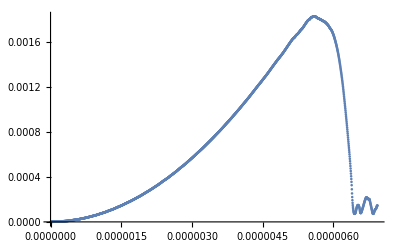

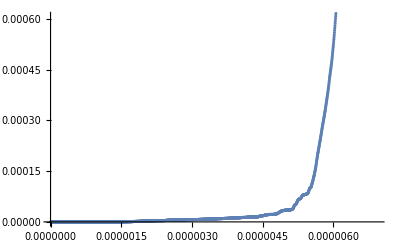

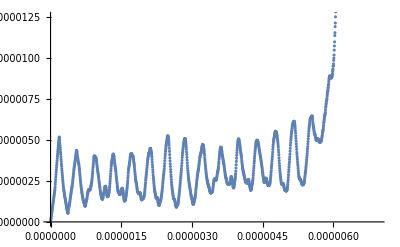

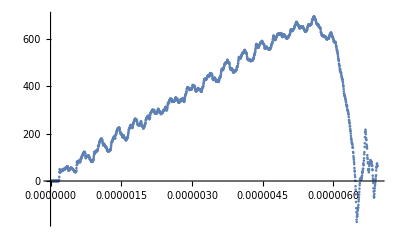

```mathematica
ListPlot[{timeList,strainEnergy/1000}ᵀ]
ListPlot[{timeList,(pfEnergy-pfEnergy[[3]])/1000}ᵀ]
ListPlot[{timeList,KineticEnergy/1000}ᵀ]
ListPlot[{timeList,reactionForceList[[All,2]]/1000}ᵀ]
```

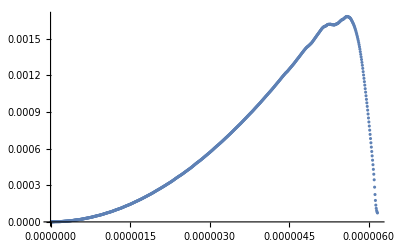

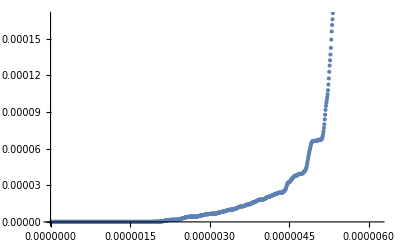

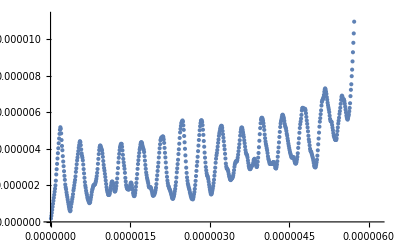

```mathematica
1.25dx,1G
```

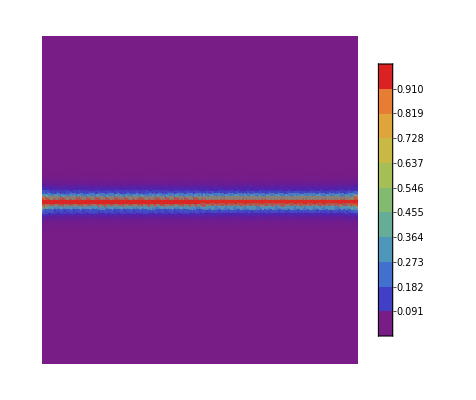

```mathematica
Plot2DField[uvw[[All,2]],mesh1]
Plot2DField[velo[[All,2]],mesh1]
Plot2DField[pfList,mesh1](*1.25dx*)
```